```mathematica
SetDirectory@NotebookDirectory[];
```

## Parameters

```mathematica
nMax=30;
χ=1./8.;
```

## Cost upper bound

```mathematica
nList={};
cList={};
Do[(
AppendTo[nList,n];
If[n==0,factor=1.,factor=(n/Exp[1.])^(-n/2)];
cost=NIntegrate[2(2^(-n/2)Abs[HermiteH[n,u/(√2)]] 1/(√(2π))Exp[-(1/2-χ)u^2])*factor,{u,0.,∞}];
AppendTo[cList,cost]
),{n,0,nMax}]
```

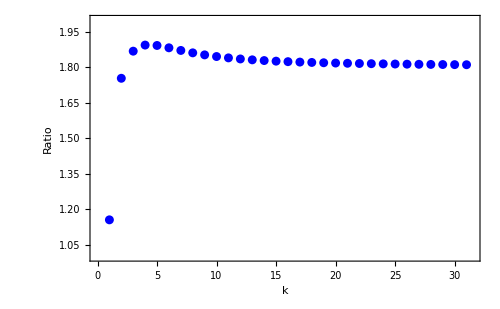

{1.1547,1.75399,1.86875,1.89461,1.89291,1.88305,1.87188,1.86169,1.8531,1.84608,1.8404,1.83582,1.83209,1.82904,1.82651,1.82439,1.82259,1.82105,1.81971,1.81854,1.81751,1.8166,1.81578,1.81504,1.81437,1.81376,1.81321,1.8127,1.81223,1.81179,1.81139}

```mathematica
PR={{0,31.5},{1,2}};
ListPlot[Transpose[{nList+1,cList}],PlotRange->PR,PlotStyle->{Blue},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"k","Ratio"},LabelStyle->Directive[Black,FontSize->18,FontFamily->"Arial"],ImageSize->500]
cList
```